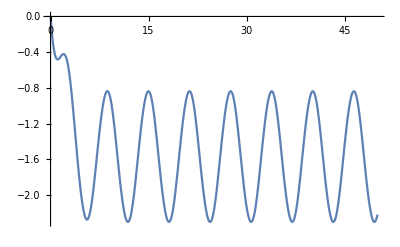

```mathematica
f[x_,y_]= Sin[x]-Cos[y];
u0=0;h=1.5;T=50;
ndsol = NDSolve[{u'[x]==f[x,u[x]],u[0]==u0},u[x],{x,0,T}];
pl = Plot[u[x]/.ndsol,{x,0,T}]
```

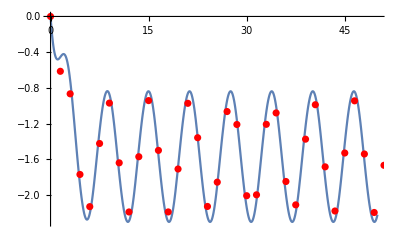

```mathematica
coefficients[xList_]:=(
  n1=Length[xList];
	basis=Table[0,n1];
	For[s=1,s≤n1,s++,numerator=Product[x-xList[[k]],{k,Range[n1]}]/(x-xList[[s]]);
denominator=numerator/. x->xList[[s]];
basis[[s]]=numerator/denominator;];
Return[Integrate[basis,{x,0,1}]];
);
AdamsPredictorCorrector2[f_,u0_,h_,T_,coeffs1_,coeffs2_,k_]:=(
n = Ceiling[T/h];
xList=Table[i*h,{i,0,n}];
yList = Table[0,n+1];
fList = Table[0,n+1];
yList[[1]] = u0;
fList[[1]] = f[xList[[1]],yList[[1]]];

yList[[2]] = Y/.FindRoot[Y==yList[[1]]+h/2(f[xList[[1]],yList[[1]]] +f[xList[[2]],Y]),{Y,yList[[1]]}];

fList[[2]] = f[xList[[2]],yList[[2]]];
For[i=2,i≤n,i++,
yNext = yList[[i]] + h coeffs1[[1]] *fList[[i-1]] + h coeffs1[[2]]*fList[[i]];
For[j= 1,j≤k,j++,
yNext = yList[[i]] + h coeffs2[[1]] *fList[[i]] + h coeffs2[[2]]*f[xList[[i+1]],yNext];
];
yList[[i+1]] = yNext;
fList[[i+1]] = f[xList[[i+1]],yList[[i+1]]];
];
Return[Transpose[{xList,yList}]];
);
apc2 = AdamsPredictorCorrector2[f,u0,h,T,coefficients[{-1,0}],coefficients[{0,1}],7];
lp3 = ListPlot[apc2,PlotStyle->Red];
Show[pl,lp3]
```

```mathematica
T=20;x0=1;y0=-1;h=0.01;
ndsol = NDSolve[{x'[t] == x[t] - 2 y[t],y'[t] == 2x[t] - y[t],x[0]==x0,y[0] == y0},{x[t],y[t]},{t,0,T}];
pl = ParametricPlot3D[{t,x[t],y[t]}/.ndsol,{t,0,20}]
```

```mathematica
f[x_,y_] := {x-2y,2x-y};
Euler[f_,x0_,y0_,h_,T_]:=(
n = Ceiling[T/h];
x = Table[0,n+1];
y = Table[0,n+1];
x[[1]] = x0;
y[[1]] = y0;
For[i = 1;i≤n;i++,
x[i+1] = x[i] + h*f[[1]][ih];

]
);
```